# Lexical Analyzer

## Token symbols recognizer

```mathematica
Token[symbol_String,name_String]:=<|"Class"->"Token","Symbol"->symbol,"Name"->name|>;
```

```mathematica
TokenKeyword[symbol_String,name_String]:=<|"Class"->"TokenKeyword","Symbol"->symbol,"Name"->name|>;
```

```mathematica
tokenSymbols = Map[
Token[#[[1]],#[[2]]]&,
{
{"end of file","EndOfFile"},
{" ","Whitespace"},
{":=", "Assign"},
{"*", "Asterisk"},
{":", "Colon"},
{"!=", "Different"},
{"=", "Equal"},
{"(", "LeftParenthesis"},
{"-", "Minus"},
{"+", "Plus"},
{")", "RightParenthesis"},
{";", "Semicolon"},
{"/", "Slash"},
{"%", "Percent"},
{">", "Greater"},
{">=", "GreaterOrEqual"},
{"<", "Lower"},
{"<=", "LowerOrEqual"},
{"#", "LineComment"},
{"\n", "LineBreak"}
}
];
tokenIdentifiersAndLiterals = Map[
Token[#[[1]],#[[2]]]&,
{
{"identifier", "Identifier"},
{"integer literal", "IntegerLiteral"},
{"real literal", "RealLiteral"},
{"string literal", "StringLiteral"}
}
];

tokenKeywords = Map[
TokenKeyword[#[[1]],#[[2]]]&,
{
{"and","And"},
{"do", "Do"},
{"else", "Else"},
{"end", "End"},
{"float", "Float"},
{"for", "For"},
{"if", "If"},
{"int", "Int"},
{"not", "Not"},
{"or", "Or"},
{"read", "Read"},
{"then", "Then"},
{"to", "To"},
{"var", "Var"},
{"while", "While"},
{"write", "Write"}
}
];
```

```mathematica
tokenSymbolsNFA = SimplifyMachine[Apply[RegexUnion,Map[Regex[#["Symbol"],#["Name"]]&,tokenSymbols]]];
tokenSymbolsDFA = NFAToDFA[tokenSymbolsNFA];

identifierRegex =RegexConcatenation[RegexAlphabet[],RegexStar[RegexUnion[RegexAlphabet[],RegexDigits[]]]];
integerLiteral = RegexConcatenation[RegexDigits[],RegexStar[RegexDigits[]]];
realLiteral = RegexConcatenation[RegexStar[RegexDigits[]],Regex["."],RegexStar[RegexDigits[]]];
stringLiteral = RegexConcatenation[Regex["\""],RegexStar[RegexASCIIChars[]],Regex["\""]];

identifierRegex = Regex[identifierRegex,"Identifier"];
integerLiteral = Regex[integerLiteral,"IntegerLiteral"];
realLiteral = Regex[realLiteral,"RealLiteral"];
stringLiteral = Regex[stringLiteral, "StringLiteral"];
symbolTokens= RegexUnion[identifierRegex,integerLiteral,realLiteral,stringLiteral,tokenSymbolsDFA];
```

```mathematica
keywordNFA = SimplifyMachine[Apply[RegexUnion,Map[Regex[#["Symbol"],#["Name"]]&,tokenKeywords]]];
keywordDFA = NFAToDFA[keywordNFA];
```

```mathematica
RegexCompute[keywordDFA,"if"]
```

{{<|Node→1|>,<|Parent→1,Node→11,InputSymbol→{i}|>,<|Parent→11,Node→26,InputSymbol→{f}|>},True,{If}}

## Tokenizer

```mathematica
tinyProgram ="var i : int;
for i := 0 to 10 do     # this is a comment
   write i;
end";
```

```mathematica
GetToken[input_,symbolTokens_,keywordTokens_]:=Block[{symbolAccept,symbolResult,keywordAccept,keywordResult},
{symbolAccept,symbolResult} = Rest[RegexCompute[symbolTokens,input]];
{keywordAccept,keywordResult} = Quiet[Rest[RegexCompute[keywordTokens,input]]];
If[keywordAccept,Return[First[keywordResult]]];
If[symbolAccept,Return[First[symbolResult]]];
Return["Nothing"];
];

SafeStringTake[string_,n_]:=StringTake[string,Min[n,StringLength[string]]];
SafeStringTake[string_,{m_,n_}]:=StringTake[string,{m,Min[n,StringLength[string]]}];

GetNextToken[program_,symbolTokens_,keywordTokens_]:=Block[{tokenizerResult,nextToken},
tokenizerResult = NestWhileList[
{
First[#]+1,
GetToken[SafeStringTake[program,First[#]+1],symbolTokens,keywordTokens]
}&,
{
0,
None
},
((Last[#]=!= "Nothing")&&(First[#]≤StringLength[program]))&
];

nextToken = If[Length[tokenizerResult]>2,tokenizerResult[[-2]],Last[tokenizerResult]];
Return[nextToken];
];

SafeMod[m_,0]:=m;
SafeMod[m_,n_]:=Mod[m,n];
LinePosition[pos_,lineBreaks_]:=SafeMod[pos,Last[Select[Prepend[lineBreaks+1, 0],#≤pos&]]];
ColumnPosition[pos_,lineBreaks_]:=Position[Ordering[Prepend[lineBreaks, pos]],1][[1,1]]-1;

Options[Tokenize]={"IncludeLineBreaks"->False};
Tokenize[program_,symbolTokens_,keywordTokens_,OptionsPattern[]]:=Block[
{
length,type,
cursor = 0,
tokenList = {},
inComment = False,
omitTokens = {"Whitespace","LineComment"},
breaks,positionMappedTokens,formattedTokens
},

While[cursor<StringLength[program],
{length,type} = GetNextToken[StringDrop[program,cursor],symbolTokens,keywordTokens];
If[inComment,
If[type == "LineBreak",
AppendTo[tokenList,<|"Position"->cursor,"Type"->type,"Value"->SafeStringTake[program,{cursor,cursor+length-1}+1]|>];
inComment = False;
];
,

If[!MemberQ[omitTokens,type],
AppendTo[tokenList,<|"Position"->cursor,"Type"->type,"Value"->SafeStringTake[program,{cursor,cursor+length-1}+1]|>];
];
];
cursor+=length;
If[type == "LineComment",inComment = True];
];

breaks = Cases[tokenList,KeyValuePattern[{"Position"->p_,"Type"->"LineBreak"}]:>p];
positionMappedTokens = Map[
<|
"From"->#["Position"],
"To"->#["Position"]+StringLength[#["Value"]],
"Column"->ColumnPosition[#["Position"],breaks],
"Line"->LinePosition[#["Position"],breaks],
"Type"->#["Type"],
"Value"->#["Value"]
|>&,
tokenList
];
If[OptionValue["IncludeLineBreaks"],
Return[positionMappedTokens];
,
formattedTokens = DeleteCases[positionMappedTokens,KeyValuePattern["Type"->"LineBreak"]];
Return[formattedTokens];
];
];

Lint[program_,symbolTokens_,keywordTokens_]:=Block[{tokens,colorRules,highlighted,linted},
colorRules = {
"Var"->LightBlue,
"Identifier"->LightYellow,
"Int"->LightGreen,
"For"->LightCyan,
"To"->LightOrange,
"Do"->LightPink,
"End"->LightGray,
"Write"->LightBrown,
"IntegerLiteral"->LightRed
};
tokens = Tokenize[program,symbolTokens,keywordTokens];
highlighted = Map[Highlighted[#["Value"],Background-> (#["Type"]/.colorRules)]&,tokens];
linted = Row@Prepend[Riffle[highlighted," "]," "];
Return[linted];
];
```

```mathematica
GetToken["108745.0304",symbolTokens,keywordDFA]
```

RealLiteral

```mathematica
GetNextToken[tinyProgram,symbolTokens,keywordDFA]
```

{3,Var}

```mathematica
GetNextToken[StringDrop[tinyProgram,3],symbolTokens,keywordDFA]
```

{1,Whitespace}

```mathematica
GetNextToken[StringDrop[tinyProgram,4],symbolTokens,keywordDFA]
```

{1,Identifier}

```mathematica
tinyProgram
```

var i : int;
for i := 0 to 10 do     # this is a comment
   write i;
end

```mathematica
tokens = Tokenize[tinyProgram,symbolTokens,keywordDFA]
```

{<|From→0,To→3,Column→0,Line→0,Type→Var,Value→var|>,<|From→4,To→5,Column→0,Line→4,Type→Identifier,Value→i|>,<|From→6,To→7,Column→0,Line→6,Type→Colon,Value→:|>,<|From→8,To→11,Column→0,Line→8,Type→Int,Value→int|>,<|From→11,To→12,Column→0,Line→11,Type→Semicolon,Value→;|>,<|From→13,To→16,Column→1,Line→0,Type→For,Value→for|>,<|From→17,To→18,Column→1,Line→4,Type→Identifier,Value→i|>,<|From→19,To→21,Column→1,Line→6,Type→Assign,Value→:=|>,<|From→22,To→23,Column→1,Line→9,Type→IntegerLiteral,Value→0|>,<|From→24,To→26,Column→1,Line→11,Type→To,Value→to|>,<|From→27,To→29,Column→1,Line→1,Type→IntegerLiteral,Value→10|>,<|From→30,To→32,Column→1,Line→4,Type→Do,Value→do|>,<|From→60,To→65,Column→2,Line→3,Type→Write,Value→write|>,<|From→66,To→67,Column→2,Line→9,Type→Identifier,Value→i|>,<|From→67,To→68,Column→2,Line→10,Type→Semicolon,Value→;|>,<|From→69,To→72,Column→3,Line→0,Type→End,Value→end|>}

```mathematica
Lint[tinyProgram,symbolTokens,keywordDFA]
```

var i : int ; for i := 0 to 10 do write i ; end

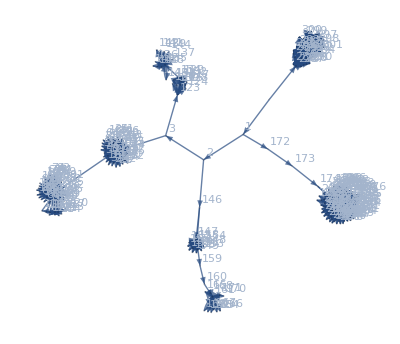

```mathematica
FAPlot[symbolTokens,"Labeled"->False]
```

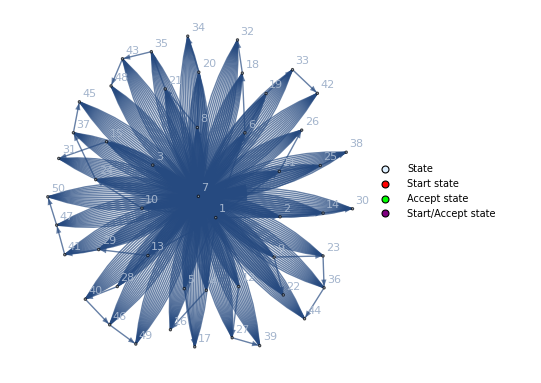

```mathematica
FAPlot[keywordDFA,"Labeled"->False]
```